```mathematica
years = {1902,1907,1912,1917}; population = {1174700,1345700,1617157,1854400}
```

{1174700,1345700,1617157,1854400}

```mathematica
x = Map[Function[xi, xi-1900], years]; y = Map[ Function[yi, yi/ 1000000], population]
```

{11747/10000,13457/10000,1617157/1000000,1159/625}

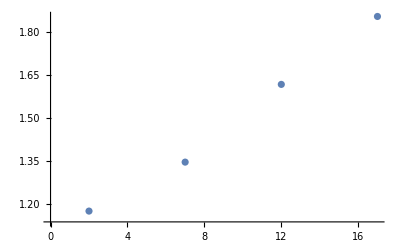

```mathematica
ListPlot[Table[{x[[i]], y[[i]]},{i,4}]]
```

```mathematica
F[a_,b_,c_,d_]:=Sum[(yi-a xi^3-b xi^2-c xi-d)^2, {i, 4}]
```

```mathematica
Print[D[F[a,b,c,d],a]==0];
Print[D[F[a,b,c,d],b]==0];
Print[D[F[a,b,c,d],c]==0];
Print[D[F[a,b,c,d],d]==0]
```

-8 xi^3 (-d-c xi-b xi^2-a xi^3+yi)==0

-8 xi^2 (-d-c xi-b xi^2-a xi^3+yi)==0

-8 xi (-d-c xi-b xi^2-a xi^3+yi)==0

-8 (-d-c xi-b xi^2-a xi^3+yi)==0

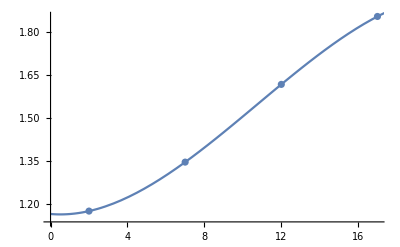

```mathematica
Show[ListPlot[Table[{x[[i]], y[[i]]},{i,4}]],Plot[-0.00017956133333323724 t^3 +0.005779927999997216 t^2-0.005788742666644684t+1.1645942639999614,{t,0,20}]]
```

```mathematica
-0.00017956133333323724 t^3 +0.005779927999997216 t^2-0.005788742666644684t+1.1645942639999614 /.t->10
```

1.50514

```mathematica
-0.00017956133333323724 t^3 +0.005779927999997216 t^2-0.005788742666644684t+1.1645942639999614 /.t->16
```

1.81615